/homes/ht/Desktop/today2/dev/large_etab_code_MASTER/results/Intact

{{L:,60.2},{m:,150},{N:,13},{kappa:,0.1},{sigma:,0.0012},{kappa_sigma_r:,83.3333},{Delta:,0.2},{Extension Minimum:,0},{Extension Maximum:,1},{e0:,0.04},{Beta:,38.6817}}

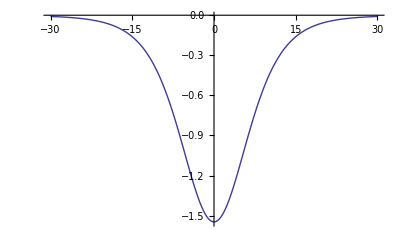

Backbone spring constant κ:

0.1

Base-pair spring constant σ(ϵ = 0.04):

0.0012

κ/σ ratio:

83.3333

```mathematica
Needs["PlotLegends`"]
<<Units`
<<PhysicalConstants`

SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["../Parameters"]
Potential=Import["../Potential_Data.out","Table"];
ListLinePlot[Potential,PlotStyle->{Thick},AxesOrigin->{0,0},PlotRange->All]

IntactPF=Import["PartitionFunction_0_0.out","Table"];
IntactFE=Import["FreeEnergy_0_0.out","Table"];
IntactdFE=Import["dFreeEnergy_0_0.out","Table"];

IntactZNJη=Import["znj_eta.out","Table"];
IntactZNJξ=Import["znj_xi.out","Table"];

IntactMXDη=Import["MeanAxialDisp_eta.out","Table"];
IntactMXDξ=Import["MeanAxialDisp_xi.out","Table"];

AverageX= Import["Average_X.out","Table"];
AverageY= Import["Average_Y.out","Table"];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

T=300 SI[Kelvin];
n=Parameters[[3,2]];
Print["Backbone spring constant κ:"]
κ=Parameters[[4,2]]
Print["Base-pair spring constant σ(ϵ = "<>ToString[ϵ]<>"):"]
σ=Parameters[[5,2]]
Print["κ/σ ratio:"]
κσr=Parameters[[6,2]]
Δ=Parameters[[7,2]];

umin=Parameters[[8,2]];
umax=Parameters[[9,2]];

ϵ=Parameters[[10,2]];(*eV*)
β=Parameters[[11,2]];(*eV^-1*) 

Subscript[η, B]=2.0;
ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1 ;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f(κ/(4β))^(1/2)) ToNewton;
ToDimension[η_]:=η((κ β)/4)^(-1/2)(*Converts to Å*)
```

### Length Dimension Check

```mathematica
Subscript[η, B] (*No Dimension*)
ToDimension[Subscript[η, B]] (*Å*)
```

2.

2.0338

### Force Dimension Check

```mathematica
0.5 (*No Dimension*)
σ ToDimension[Subscript[η, B]] ToNewton  (*pN*)
ToForceDimension[0.5] (*Converts force to dimensions of eV/Å then to J/m for pN*)
```

0.5

3.9102

20.3656

## Numerical Results

### Partition Function & Free Energy

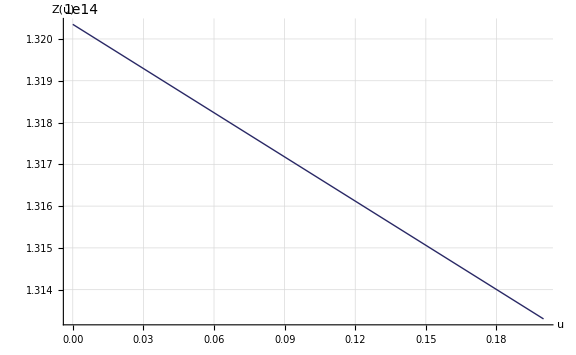
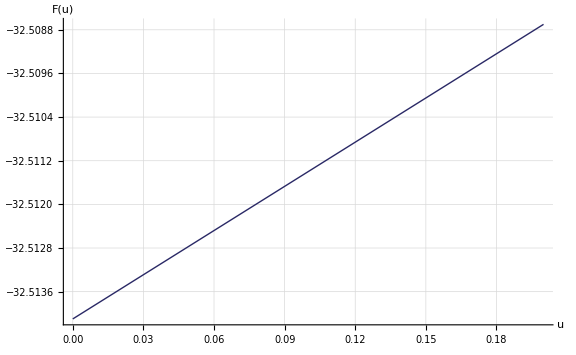

```mathematica
pIntactPF=ListLinePlot[
IntactPF,
ImageSize->Large,
PlotStyle->{Thick,Darker[ColorData[1,1]]},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->All,
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["Z(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
];

pIntactFE=ListLinePlot[
IntactFE,
ImageSize->Large,
PlotStyle->{Thick,Darker[ColorData[1,1]]},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->All,
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["F(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
];

{pIntactPF,pIntactFE}
```

### Mean Axial Displacement of ξ and η

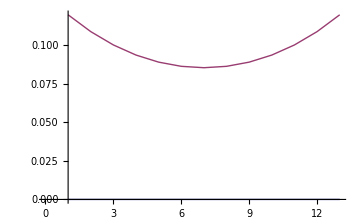
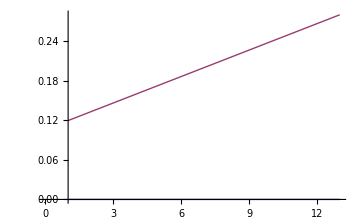

0.119722

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.119722 | 0.108813 | 0.100167 | 0.0936136 | 0.089024 | 0.0863065 | 0.0854067 | 0.0863065 | 0.089024 | 0.0936136 | 0.100167 | 0.108813 | 0.119722

Extension U (End base-pair separations at η_B) = 1

Extension U in terms of η = 0.2 (1Δ)

```mathematica
{ListLinePlot[IntactMXDη,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],
ListLinePlot[IntactMXDξ,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
NearestValue=Nearest[Transpose[Chop[IntactMXDη,10^-5]][[1]],Subscript[η, B]][[1]]
upos=Flatten[Position[Transpose[Chop[IntactMXDη,10^-5]][[1]],NearestValue]][[1]];
U=upos-1;
Grid[Chop[IntactMXDη,10^-5],Background->{Automatic,{upos->Yellow}}]
Print["Extension U (End base-pair separations at η_B) = ",U]
Print["Extension U in terms of η = ",U Δ," (",U,"Δ)"]
```

```mathematica
pos1=upos-2;
pos2=upos-1;
pos3=upos;
pos4=upos+1;
pos5=upos+2;

pIntactMXDη=ListLinePlot[
{
IntactMXDη[[pos1]],
IntactMXDη[[pos2]],
IntactMXDη[[pos3]],
IntactMXDη[[pos4]],
IntactMXDη[[pos5]]
},
ImageSize->1000,
PlotStyle->{
{Thick,Darker[ColorData[1,1]]},
{Thick,Red},
{Thick,Dashed,Orange},
{Thick,Purple},
{Thick,Darker[Green,0.5]}
},
PlotLegend->{
Style["u="<>ToString[(pos1-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos2-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos3-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos4-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos5-1)Δ],FontSize->fs2]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
PlotRange->All,
AxesOrigin->{1,0},
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨η_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->0.55,
LegendPosition->{0.9,-.2}
]

pIntactMXDξ=ListLinePlot[
{
IntactMXDξ[[pos1]],
IntactMXDξ[[pos2]],
IntactMXDξ[[pos3]],
IntactMXDξ[[pos4]],
IntactMXDξ[[pos5]]
},
ImageSize->1000,
PlotStyle->{
{Thick,Darker[ColorData[1,1]]},
{Thick,Red},
{Thick,Dashed,Orange},
{Thick,Purple},
{Thick,Darker[Green,0.5]}
},
PlotLegend->{
Style["u="<>ToString[(pos1-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos2-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos3-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos4-1)Δ],FontSize->fs2],
Style["u="<>ToString[(pos5-1)Δ],FontSize->fs2]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
PlotRange->All,
AxesOrigin->{1,0},
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨ξ_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->0.55,
LegendPosition->{0.9,-.2}
]
```

Part::partw: Part 3 of {{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, 2.26148`*^-15, 2.38112`*^-15, 2.44685`*^-15, 2.46788`*^-15, 2.44709`*^-15, 2.38159`*^-15, 2.26214`*^-15, 2.07147`*^-15, 1.78048`*^-15, 1.34137`*^-15}, {0.119722`, 0.108813`, 0.100167`, 0.0936136`, 0.089024`, 0.0863065`, 0.0854067`, 0.0863065`, 0.089024`, 0.0936136`, 0.100167`, 0.108813`, 0.119722`}} does not exist.

Part::partw: Part 4 of {{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, 2.26148`*^-15, 2.38112`*^-15, 2.44685`*^-15, 2.46788`*^-15, 2.44709`*^-15, 2.38159`*^-15, 2.26214`*^-15, 2.07147`*^-15, 1.78048`*^-15, 1.34137`*^-15}, {0.119722`, 0.108813`, 0.100167`, 0.0936136`, 0.089024`, 0.0863065`, 0.0854067`, 0.0863065`, 0.089024`, 0.0936136`, 0.100167`, 0.108813`, 0.119722`}} does not exist.

PadRight::ilsm: List of machine-size integers expected at position 2 in PadRight[{StyleBox[.

Part::partw: Part 3 of {{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, 2.26148`*^-15, 2.38112`*^-15, 2.44685`*^-15, 2.46788`*^-15, 2.44709`*^-15, 2.38159`*^-15, 2.26214`*^-15, 2.07147`*^-15, 1.78048`*^-15, 1.34137`*^-15}, {0.119722`, 0.108813`, 0.100167`, 0.0936136`, 0.089024`, 0.0863065`, 0.0854067`, 0.0863065`, 0.089024`, 0.0936136`, 0.100167`, 0.108813`, 0.119722`}} does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

PadRight::ilsm: List of machine-size integers expected at position 2 in PadRight[{StyleBox[.

Table::iterb: Iterator {PlotLegends`Private`i, 1, 2 + PlotLegends`Private`datasetLength[List, Automatic] + PlotLegends`Private`datasetLength[{{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, 2.26148`*^-15, 2.38112`*^-15, 2.44685`*^-15, 2.46788`*^-15, 2.44709`*^-15, 2.38159`*^-15, 2.26214`*^-15, 2.07147`*^-15, 1.78048`*^-15, 1.34137`*^-15}, « 1 »} ⟦ 3 ⟧, « 9 »] + PlotLegends`Private`datasetLength[{{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, 2.26148`*^-15, 2.38112`*^-15, 2.44685`*^-15, 2.46788`*^-15, 2.44709`*^-15, 2.38159`*^-15, 2.26214`*^-15, 2.07147`*^-15, 1.78048`*^-15, 1.34137`*^-15}, {0.119722`, 0.108813`, 0.100167`, 0.0936136`, 0.089024`, 0.0863065`, 0.0854067`, 0.0863065`, 0.089024`, 0.0936136`, 0.100167`, 0.108813`, 0.119722`}} ⟦ 4 ⟧, Automatic]} does not have appropriate bounds.

PadRight::ilsm: List of machine-size integers expected at position 2 in PadRight[{{Thickness[Large], RGBColor[0.1648000000000001`, 0.16`, 0.4`]}, {Thickness[Large], RGBColor[1, 0, 0]}, {Thickness[Large], Dashing[{Small, Small}], RGBColor[1, 0.5`, 0]}, {Thickness[Large], RGBColor[0.5`, 0, 0.5`]}, {Thickness[Large], RGBColor[0.`, 0.5`, 0.`]}}, 2 + « 1 » + « 1 » + PlotLegends`Private`datasetLength[{{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, 2.26148`*^-15, 2.38112`*^-15, « 4 », 2.26214`*^-15, 2.07147`*^-15, 1.78048`*^-15, 1.34137`*^-15}, {« 1 »}} ⟦ 4 ⟧, « 9 »], {{Thickness[Large], RGBColor[0.1648000000000001`, 0.16`, 0.4`]}, {Thickness[Large], RGBColor[1, 0, 0]}, {Thickness[Large], Dashing[{Small, Small}], RGBColor[1, 0.5`, 0]}, {Thickness[Large], RGBColor[0.5`, 0, 0.5`]}, {Thickness[Large], RGBColor[0.`, 0.5`, 0.`]}}].

General::stop: Further output of PadRight will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list {Table[Hue[FractionalPart[0.67`  + 2.` (PlotLegends`Private`i - 1)/GoldenRatio], 0.6`, 0.6`], {PlotLegends`Private`i, 1, 2 + PlotLegends`Private`datasetLength[List, Automatic] + PlotLegends`Private`datasetLength[{{« 13 »}, {« 13 »}} ⟦ 3 ⟧, Automatic] + PlotLegends`Private`datasetLength[{{« 13 »}, {« 13 »}} ⟦ 4 ⟧, Automatic]}], PadRight[{{Thickness[Large], RGBColor[0.1648000000000001`, 0.16`, 0.4`]}, {Thickness[Large], RGBColor[1, 0, 0]}, {Thickness[Large], Dashing[{Small, Small}], RGBColor[1, 0.5`, 0]}, {Thickness[Large], RGBColor[0.5`, 0, 0.5`]}, {Thickness[Large], RGBColor[0.`, 0.5`, 0.`]}}, 2 + « 2 » + PlotLegends`Private`datasetLength[{{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, « 8 », 1.78048`*^-15, 1.34137`*^-15}, {« 1 »}} ⟦ 4 ⟧, « 9 »], « 1 »]} cannot be transposed.

Table::iterb: Iterator {PlotLegends`Private`n, 2 + PlotLegends`Private`datasetLength[List, Automatic] + PlotLegends`Private`datasetLength[{{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, 2.26148`*^-15, 2.38112`*^-15, 2.44685`*^-15, 2.46788`*^-15, 2.44709`*^-15, 2.38159`*^-15, 2.26214`*^-15, 2.07147`*^-15, 1.78048`*^-15, 1.34137`*^-15}, « 1 »} ⟦ 3 ⟧, « 9 »] + PlotLegends`Private`datasetLength[{{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, 2.26148`*^-15, 2.38112`*^-15, 2.44685`*^-15, 2.46788`*^-15, 2.44709`*^-15, 2.38159`*^-15, 2.26214`*^-15, 2.07147`*^-15, 1.78048`*^-15, 1.34137`*^-15}, {0.119722`, 0.108813`, 0.100167`, 0.0936136`, 0.089024`, 0.0863065`, 0.0854067`, 0.0863065`, 0.089024`, 0.0936136`, 0.100167`, 0.108813`, 0.119722`}} ⟦ 4 ⟧, Automatic]} does not have appropriate bounds.

General::stop: Further output of Table will be suppressed during this calculation.

ListLinePlot::lpn: {List, « 3 », {{1.34084`*^-15, 1.7797`*^-15, 2.07067`*^-15, 2.26148`*^-15, 2.38112`*^-15, 2.44685`*^-15, 2.46788`*^-15, 2.44709`*^-15, 2.38159`*^-15, 2.26214`*^-15, 2.07147`*^-15, 1.78048`*^-15, 1.34137`*^-15}, {0.119722`, 0.108813`, 0.100167`, 0.0936136`, 0.089024`, 0.0863065`, 0.0854067`, 0.0863065`, 0.089024`, 0.0936136`, 0.100167`, 0.108813`, 0.119722`}} ⟦ 4 ⟧} is not a list of numbers or pairs of numbers.

ShowLegend[ListLinePlot[{List,{1.34084×10^-15,1.7797×10^-15,2.07067×10^-15,2.26148×10^-15,2.38112×10^-15,2.44685×10^-15,2.46788×10^-15,2.44709×10^-15,2.38159×10^-15,2.26214×10^-15,2.07147×10^-15,1.78048×10^-15,1.34137×10^-15},{0.119722,0.108813,0.100167,0.0936136,0.089024,0.0863065,0.0854067,0.0863065,0.089024,0.0936136,0.100167,0.108813,0.119722},{{1.34084×10^-15,1.7797×10^-15,2.07067×10^-15,2.26148×10^-15,2.38112×10^-15,2.44685×10^-15,2.46788×10^-15,2.44709×10^-15,2.38159×10^-15,2.26214×10^-15,2.07147×10^-15,1.78048×10^-15,1.34137×10^-15},{0.119722,0.108813,0.100167,0.0936136,0.089024,0.0863065,0.0854067,0.0863065,0.089024,0.0936136,0.100167,0.108813,0.119722}}⟦3⟧,{{1.34084×10^-15,1.7797×10^-15,2.07067×10^-15,2.26148×10^-15,2.38112×10^-15,2.44685×10^-15,2.46788×10^-15,2.44709×10^-15,2.38159×10^-15,2.26214×10^-15,2.07147×10^-15,1.78048×10^-15,1.34137×10^-15},{0.119722,0.108813,0.100167,0.0936136,0.089024,0.0863065,0.0854067,0.0863065,0.089024,0.0936136,0.100167,0.108813,0.119722}}⟦4⟧},DisplayFunction:>$DisplayFunction,DisplayFunction→Identity,{ImageSize→1000,PlotStyle→{{Thickness[Large],RGBColor[0.1648,0.16,0.4]},{Thickness[Large],RGBColor[1,0,0]},{Thickness[Large],Dashing[{Small,Small}],RGBColor[1,0.5,0]},{Thickness[Large],RGBColor[0.5,0,0.5]},{Thickness[Large],RGBColor[0.,0.5,0.]}},GridLines→Automatic,GridLinesStyle→Directive[GrayLevel[0.85],Dashing[{Small,Small}]],PlotRange→All,AxesOrigin→{1,0},AxesLabel→{j,⟨η_j⟩},LabelStyle→{Times,FontSize→16}}],{Table[{-Graphics-,PlotLegends`Private`txt$1764⟦PlotLegends`Private`n⟧},{PlotLegends`Private`n,2+PlotLegends`Private`datasetLength[List,Automatic]+PlotLegends`Private`datasetLength[{{1.34084×10^-15,1.7797×10^-15,2.07067×10^-15,2.26148×10^-15,2.38112×10^-15,2.44685×10^-15,2.46788×10^-15,2.44709×10^-15,2.38159×10^-15,2.26214×10^-15,2.07147×10^-15,1.78048×10^-15,1.34137×10^-15},{0.119722,0.108813,0.100167,0.0936136,0.089024,0.0863065,0.0854067,0.0863065,0.089024,0.0936136,0.100167,0.108813,0.119722}}⟦3⟧,Automatic]+PlotLegends`Private`datasetLength[{{1.34084×10^-15,1.7797×10^-15,2.07067×10^-15,2.26148×10^-15,2.38112×10^-15,2.44685×10^-15,2.46788×10^-15,2.44709×10^-15,2.38159×10^-15,2.26214×10^-15,2.07147×10^-15,1.78048×10^-15,1.34137×10^-15},{0.119722,0.108813,0.100167,0.0936136,0.089024,0.0863065,0.0854067,0.0863065,0.089024,0.0936136,0.100167,0.108813,0.119722}}⟦4⟧,Automatic]}],{ShadowBackground→Opacity[0]},{LegendShadow→None,LegendBorder→None,LegendBackground→Opacity[0],LegendSize→0.55,LegendPosition→{0.9,-0.2}}},DisplayFunction:>$DisplayFunction,AbsoluteOptions[ListLinePlot[{List,{1.34084×10^-15,1.7797×10^-15,2.07067×10^-15,2.26148×10^-15,2.38112×10^-15,2.44685×10^-15,2.46788×10^-15,2.44709×10^-15,2.38159×10^-15,2.26214×10^-15,2.07147×10^-15,1.78048×10^-15,1.34137×10^-15},{0.119722,0.108813,0.100167,0.0936136,0.089024,0.0863065,0.0854067,0.0863065,0.089024,0.0936136,0.100167,0.108813,0.119722},{{1.34084×10^-15,1.7797×10^-15,2.07067×10^-15,2.26148×10^-15,2.38112×10^-15,2.44685×10^-15,2.46788×10^-15,2.44709×10^-15,2.38159×10^-15,2.26214×10^-15,2.07147×10^-15,1.78048×10^-15,1.34137×10^-15},{0.119722,0.108813,0.100167,0.0936136,0.089024,0.0863065,0.0854067,0.0863065,0.089024,0.0936136,0.100167,0.108813,0.119722}}⟦3⟧,{{1.34084×10^-15,1.7797×10^-15,2.07067×10^-15,2.26148×10^-15,2.38112×10^-15,2.44685×10^-15,2.46788×10^-15,2.44709×10^-15,2.38159×10^-15,2.26214×10^-15,2.07147×10^-15,1.78048×10^-15,1.34137×10^-15},{0.119722,0.108813,0.100167,0.0936136,0.089024,0.0863065,0.0854067,0.0863065,0.089024,0.0936136,0.100167,0.108813,0.119722}}⟦4⟧},DisplayFunction:>$DisplayFunction,DisplayFunction→Identity,{ImageSize→1000,PlotStyle→{{Thickness[Large],RGBColor[0.1648,0.16,0.4]},{Thickness[Large],RGBColor[1,0,0]},{Thickness[Large],Dashing[{Small,Small}],RGBColor[1,0.5,0]},{Thickness[Large],RGBColor[0.5,0,0.5]},{Thickness[Large],RGBColor[0.,0.5,0.]}},GridLines→Automatic,GridLinesStyle→Directive[GrayLevel[0.85],Dashing[{Small,Small}]],PlotRange→All,AxesOrigin→{1,0},AxesLabel→{j,⟨η_j⟩},LabelStyle→{Times,FontSize→16}}],FormatType]]

Part::partw: Part 3 of {{2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, -3.27825`*^-16, -4.67255`*^-16, -6.0794`*^-16, -7.49737`*^-16, -8.92508`*^-16, -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, {0.119722`, 0.133102`, 0.146481`, 0.159861`, 0.173241`, 0.18662`, 0.2`, 0.21338`, 0.226759`, 0.240139`, 0.253519`, 0.266898`, 0.280278`}} does not exist.

Part::partw: Part 4 of {{2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, -3.27825`*^-16, -4.67255`*^-16, -6.0794`*^-16, -7.49737`*^-16, -8.92508`*^-16, -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, {0.119722`, 0.133102`, 0.146481`, 0.159861`, 0.173241`, 0.18662`, 0.2`, 0.21338`, 0.226759`, 0.240139`, 0.253519`, 0.266898`, 0.280278`}} does not exist.

PadRight::ilsm: List of machine-size integers expected at position 2 in PadRight[{StyleBox[.

Table::iterb: Iterator {PlotLegends`Private`i, 1, 2 + PlotLegends`Private`datasetLength[List, Automatic] + PlotLegends`Private`datasetLength[{{2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, -3.27825`*^-16, -4.67255`*^-16, -« 12 », -7.49737`*^-16, -8.92508`*^-16, -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, « 1 »} ⟦ 3 ⟧, « 9 »] + PlotLegends`Private`datasetLength[{{2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, -3.27825`*^-16, -4.67255`*^-16, -6.0794`*^-16, -7.49737`*^-16, -8.92508`*^-16, -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, {0.119722`, 0.133102`, 0.146481`, 0.159861`, 0.173241`, 0.18662`, 0.2`, 0.21338`, 0.226759`, 0.240139`, 0.253519`, 0.266898`, 0.280278`}} ⟦ 4 ⟧, Automatic]} does not have appropriate bounds.

PadRight::ilsm: List of machine-size integers expected at position 2 in PadRight[{{Thickness[Large], RGBColor[0.1648000000000001`, 0.16`, 0.4`]}, {Thickness[Large], RGBColor[1, 0, 0]}, {Thickness[Large], Dashing[{Small, Small}], RGBColor[1, 0.5`, 0]}, {Thickness[Large], RGBColor[0.5`, 0, 0.5`]}, {Thickness[Large], RGBColor[0.`, 0.5`, 0.`]}}, 2 + « 1 » + « 1 » + PlotLegends`Private`datasetLength[{{2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, « 5 », -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, {« 1 »}} ⟦ 4 ⟧, Automatic], {{Thickness[Large], RGBColor[0.1648000000000001`, 0.16`, 0.4`]}, {Thickness[Large], RGBColor[1, 0, 0]}, {Thickness[Large], Dashing[{Small, Small}], RGBColor[1, 0.5`, 0]}, {Thickness[Large], RGBColor[0.5`, 0, 0.5`]}, {Thickness[Large], RGBColor[0.`, 0.5`, 0.`]}}].

Transpose::nmtx: The first two levels of the one-dimensional list {Table[Hue[FractionalPart[0.67`  + 2.` (PlotLegends`Private`i - 1)/GoldenRatio], 0.6`, 0.6`], {PlotLegends`Private`i, 1, 2 + PlotLegends`Private`datasetLength[List, Automatic] + PlotLegends`Private`datasetLength[{{« 13 »}, {« 13 »}} ⟦ 3 ⟧, Automatic] + PlotLegends`Private`datasetLength[{{« 13 »}, {« 13 »}} ⟦ 4 ⟧, Automatic]}], PadRight[{{Thickness[Large], RGBColor[0.1648000000000001`, 0.16`, 0.4`]}, {Thickness[Large], RGBColor[1, 0, 0]}, {Thickness[Large], Dashing[{Small, Small}], RGBColor[1, 0.5`, 0]}, {Thickness[Large], RGBColor[0.5`, 0, 0.5`]}, {Thickness[Large], RGBColor[0.`, 0.5`, 0.`]}}, 2 + « 2 » + PlotLegends`Private`datasetLength[{{2.13097`*^-16, 8.10178`*^-17, « 9 », -1.32539`*^-15, -1.4709`*^-15}, {0.119722`, « 12 »}} ⟦ 4 ⟧, « 9 »], « 1 »]} cannot be transposed.

Table::iterb: Iterator {PlotLegends`Private`n, 2 + PlotLegends`Private`datasetLength[List, Automatic] + PlotLegends`Private`datasetLength[{{2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, -3.27825`*^-16, -4.67255`*^-16, -« 12 », -7.49737`*^-16, -8.92508`*^-16, -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, « 1 »} ⟦ 3 ⟧, « 9 »] + PlotLegends`Private`datasetLength[{{2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, -3.27825`*^-16, -4.67255`*^-16, -6.0794`*^-16, -7.49737`*^-16, -8.92508`*^-16, -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, {0.119722`, 0.133102`, 0.146481`, 0.159861`, 0.173241`, 0.18662`, 0.2`, 0.21338`, 0.226759`, 0.240139`, 0.253519`, 0.266898`, 0.280278`}} ⟦ 4 ⟧, Automatic]} does not have appropriate bounds.

General::stop: Further output of Table will be suppressed during this calculation.

ListLinePlot::lpn: {List, {2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, -3.27825`*^-16, -4.67255`*^-16, -6.0794`*^-16, -7.49737`*^-16, -8.92508`*^-16, -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, {« 1 »}, {{2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, -3.27825`*^-16, « 4 », -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, {« 1 »}} ⟦ 3 ⟧, {{2.13097`*^-16, 8.10178`*^-17, -5.34378`*^-17, -1.89817`*^-16, -3.27825`*^-16, -4.67255`*^-16, -6.0794`*^-16, -7.49737`*^-16, -8.92508`*^-16, -1.03612`*^-15, -1.18045`*^-15, -1.32539`*^-15, -1.4709`*^-15}, {0.119722`, 0.133102`, 0.146481`, 0.159861`, 0.173241`, 0.18662`, 0.2`, 0.21338`, 0.226759`, 0.240139`, 0.253519`, 0.266898`, 0.280278`}} ⟦ 4 ⟧} is not a list of numbers or pairs of numbers.

ShowLegend[ListLinePlot[{List,{2.13097×10^-16,8.10178×10^-17,-5.34378×10^-17,-1.89817×10^-16,-3.27825×10^-16,-4.67255×10^-16,-6.0794×10^-16,-7.49737×10^-16,-8.92508×10^-16,-1.03612×10^-15,-1.18045×10^-15,-1.32539×10^-15,-1.4709×10^-15},{0.119722,0.133102,0.146481,0.159861,0.173241,0.18662,0.2,0.21338,0.226759,0.240139,0.253519,0.266898,0.280278},{{2.13097×10^-16,8.10178×10^-17,-5.34378×10^-17,-1.89817×10^-16,-3.27825×10^-16,-4.67255×10^-16,-6.0794×10^-16,-7.49737×10^-16,-8.92508×10^-16,-1.03612×10^-15,-1.18045×10^-15,-1.32539×10^-15,-1.4709×10^-15},{0.119722,0.133102,0.146481,0.159861,0.173241,0.18662,0.2,0.21338,0.226759,0.240139,0.253519,0.266898,0.280278}}⟦3⟧,{{2.13097×10^-16,8.10178×10^-17,-5.34378×10^-17,-1.89817×10^-16,-3.27825×10^-16,-4.67255×10^-16,-6.0794×10^-16,-7.49737×10^-16,-8.92508×10^-16,-1.03612×10^-15,-1.18045×10^-15,-1.32539×10^-15,-1.4709×10^-15},{0.119722,0.133102,0.146481,0.159861,0.173241,0.18662,0.2,0.21338,0.226759,0.240139,0.253519,0.266898,0.280278}}⟦4⟧},DisplayFunction:>$DisplayFunction,DisplayFunction→Identity,{ImageSize→1000,PlotStyle→{{Thickness[Large],RGBColor[0.1648,0.16,0.4]},{Thickness[Large],RGBColor[1,0,0]},{Thickness[Large],Dashing[{Small,Small}],RGBColor[1,0.5,0]},{Thickness[Large],RGBColor[0.5,0,0.5]},{Thickness[Large],RGBColor[0.,0.5,0.]}},GridLines→Automatic,GridLinesStyle→Directive[GrayLevel[0.85],Dashing[{Small,Small}]],PlotRange→All,AxesOrigin→{1,0},AxesLabel→{j,⟨ξ_j⟩},LabelStyle→{Times,FontSize→16}}],{Table[{-Graphics-,PlotLegends`Private`txt$1801⟦PlotLegends`Private`n⟧},{PlotLegends`Private`n,2+PlotLegends`Private`datasetLength[List,Automatic]+PlotLegends`Private`datasetLength[{{2.13097×10^-16,8.10178×10^-17,-5.34378×10^-17,-1.89817×10^-16,-3.27825×10^-16,-4.67255×10^-16,-6.0794×10^-16,-7.49737×10^-16,-8.92508×10^-16,-1.03612×10^-15,-1.18045×10^-15,-1.32539×10^-15,-1.4709×10^-15},{0.119722,0.133102,0.146481,0.159861,0.173241,0.18662,0.2,0.21338,0.226759,0.240139,0.253519,0.266898,0.280278}}⟦3⟧,Automatic]+PlotLegends`Private`datasetLength[{{2.13097×10^-16,8.10178×10^-17,-5.34378×10^-17,-1.89817×10^-16,-3.27825×10^-16,-4.67255×10^-16,-6.0794×10^-16,-7.49737×10^-16,-8.92508×10^-16,-1.03612×10^-15,-1.18045×10^-15,-1.32539×10^-15,-1.4709×10^-15},{0.119722,0.133102,0.146481,0.159861,0.173241,0.18662,0.2,0.21338,0.226759,0.240139,0.253519,0.266898,0.280278}}⟦4⟧,Automatic]}],{ShadowBackground→Opacity[0]},{LegendShadow→None,LegendBorder→None,LegendBackground→Opacity[0],LegendSize→0.55,LegendPosition→{0.9,-0.2}}},DisplayFunction:>$DisplayFunction,AbsoluteOptions[ListLinePlot[{List,{2.13097×10^-16,8.10178×10^-17,-5.34378×10^-17,-1.89817×10^-16,-3.27825×10^-16,-4.67255×10^-16,-6.0794×10^-16,-7.49737×10^-16,-8.92508×10^-16,-1.03612×10^-15,-1.18045×10^-15,-1.32539×10^-15,-1.4709×10^-15},{0.119722,0.133102,0.146481,0.159861,0.173241,0.18662,0.2,0.21338,0.226759,0.240139,0.253519,0.266898,0.280278},{{2.13097×10^-16,8.10178×10^-17,-5.34378×10^-17,-1.89817×10^-16,-3.27825×10^-16,-4.67255×10^-16,-6.0794×10^-16,-7.49737×10^-16,-8.92508×10^-16,-1.03612×10^-15,-1.18045×10^-15,-1.32539×10^-15,-1.4709×10^-15},{0.119722,0.133102,0.146481,0.159861,0.173241,0.18662,0.2,0.21338,0.226759,0.240139,0.253519,0.266898,0.280278}}⟦3⟧,{{2.13097×10^-16,8.10178×10^-17,-5.34378×10^-17,-1.89817×10^-16,-3.27825×10^-16,-4.67255×10^-16,-6.0794×10^-16,-7.49737×10^-16,-8.92508×10^-16,-1.03612×10^-15,-1.18045×10^-15,-1.32539×10^-15,-1.4709×10^-15},{0.119722,0.133102,0.146481,0.159861,0.173241,0.18662,0.2,0.21338,0.226759,0.240139,0.253519,0.266898,0.280278}}⟦4⟧},DisplayFunction:>$DisplayFunction,DisplayFunction→Identity,{ImageSize→1000,PlotStyle→{{Thickness[Large],RGBColor[0.1648,0.16,0.4]},{Thickness[Large],RGBColor[1,0,0]},{Thickness[Large],Dashing[{Small,Small}],RGBColor[1,0.5,0]},{Thickness[Large],RGBColor[0.5,0,0.5]},{Thickness[Large],RGBColor[0.,0.5,0.]}},GridLines→Automatic,GridLinesStyle→Directive[GrayLevel[0.85],Dashing[{Small,Small}]],PlotRange→All,AxesOrigin→{1,0},AxesLabel→{j,⟨ξ_j⟩},LabelStyle→{Times,FontSize→16}}],FormatType]]

### Force-Extension

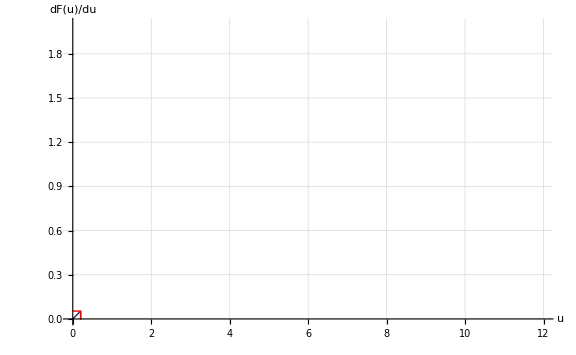

Dimensionless force at (U = 1Δ) = 0.0535188

Dimensional Force = 2.17989 pN
Dimensional Extension = 0.20338 Å

Dimensional Resultant Average Force = 2.21263 pN

```mathematica
fpos={{0,IntactdFE[[upos]][[2]]},{IntactdFE[[upos]][[1]],IntactdFE[[upos]][[2]]},{IntactdFE[[upos]][[1]],0},{IntactdFE[[upos]][[1]],IntactdFE[[upos]][[2]]}};
F=IntactdFE[[upos]][[2]];
u = IntactdFE[[upos]][[1]];

Subscript[resF, c]=(κ (ToDimension[AverageX[[upos]][[n]]-AverageX[[upos]][[n-1]]])+σ (ToDimension[AverageX[[upos]][[n]] -AverageY[[upos]][[n]]]))ToNewton;

pIntactPF=ListLinePlot[
{
IntactdFE,
fpos
},
ImageSize->Large,
PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->{{0,12},{0,2}},
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["dF(u)/du",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
]
Print["Dimensionless force at (U = ",U,"Δ) = ",F]

Subscript[F, c]=ToForceDimension[F];
Print["\nDimensional Force = ",Subscript[F, c] pN,"\nDimensional Extension = ",ToDimension[u]Å,"\n\nDimensional Resultant Average Force = ",Subscript[resF, c] pN,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Subscript[F, c],Subscript[resF, c],NearestValue,κσr}},"Table"];
```

### Average X and Y

Part::partw: Part 3 of {{7.76968`*^-16, 9.30359`*^-16, 1.00862`*^-15, 1.03583`*^-15, 1.02665`*^-15, 9.898`*^-16, 9.29972`*^-16, 8.48679`*^-16, 7.44539`*^-16, 6.13011`*^-16, 4.45507`*^-16, 2.27546`*^-16, -6.47643`*^-17}, {0.119722`, 0.120957`, 0.123324`, 0.126737`, 0.131132`, 0.136463`, 0.142703`, 0.149843`, 0.157892`, 0.166876`, 0.176843`, 0.187856`, 0.2`}} does not exist.

Part::partw: Part 3 of {{-5.6387`*^-16, -8.49341`*^-16, -1.06206`*^-15, -1.22565`*^-15, -1.35447`*^-15, -1.45705`*^-15, -1.53791`*^-15, -1.59842`*^-15, -1.63705`*^-15, -1.64913`*^-15, -1.62596`*^-15, -1.55294`*^-15, -1.40614`*^-15}, {-2.94903`*^-15, 0.0121441`, 0.0231572`, 0.0331237`, 0.0421083`, 0.0501569`, 0.0572966`, 0.0635366`, 0.0688677`, 0.0732627`, 0.0766759`, 0.0790425`, 0.0802781`}} does not exist.

Part::partw: Part 4 of {{7.76968`*^-16, 9.30359`*^-16, 1.00862`*^-15, 1.03583`*^-15, 1.02665`*^-15, 9.898`*^-16, 9.29972`*^-16, 8.48679`*^-16, 7.44539`*^-16, 6.13011`*^-16, 4.45507`*^-16, 2.27546`*^-16, -6.47643`*^-17}, {0.119722`, 0.120957`, 0.123324`, 0.126737`, 0.131132`, 0.136463`, 0.142703`, 0.149843`, 0.157892`, 0.166876`, 0.176843`, 0.187856`, 0.2`}} does not exist.

Part::partw: Part 4 of {{-5.6387`*^-16, -8.49341`*^-16, -1.06206`*^-15, -1.22565`*^-15, -1.35447`*^-15, -1.45705`*^-15, -1.53791`*^-15, -1.59842`*^-15, -1.63705`*^-15, -1.64913`*^-15, -1.62596`*^-15, -1.55294`*^-15, -1.40614`*^-15}, {-2.94903`*^-15, 0.0121441`, 0.0231572`, 0.0331237`, 0.0421083`, 0.0501569`, 0.0572966`, 0.0635366`, 0.0688677`, 0.0732627`, 0.0766759`, 0.0790425`, 0.0802781`}} does not exist.

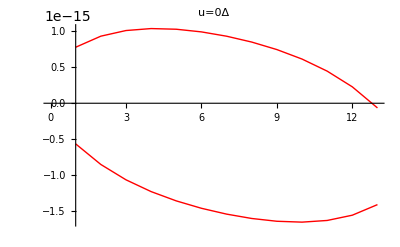
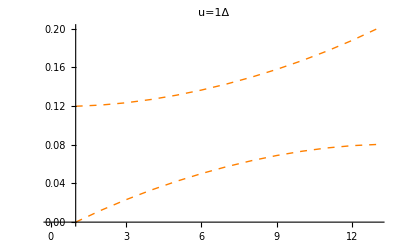
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

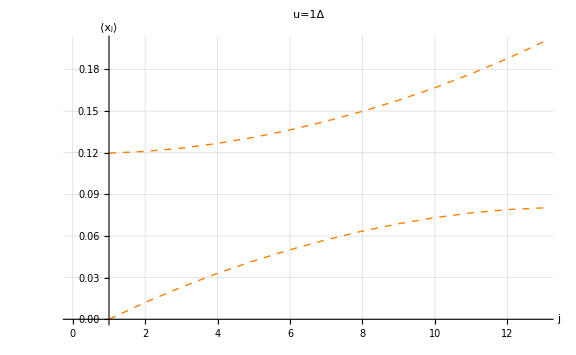

```mathematica
avg1=ListLinePlot[{Chop[AverageX[[pos1]]],Chop[AverageY[[pos1]]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Darker[Blue,0.6]}},PlotLabel->"u="<>ToString[pos1-1]<>"Δ"];
avg2=ListLinePlot[{AverageX[[pos2]],AverageY[[pos2]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Red}},PlotLabel->"u="<>ToString[pos2-1]<>"Δ"];
avg3=ListLinePlot[{AverageX[[pos3]],AverageY[[pos3]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Dashed,Orange}},PlotLabel->"u="<>ToString[pos3-1]<>"Δ"];
avg4=ListLinePlot[{AverageX[[pos4]],AverageY[[pos4]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Purple}},PlotLabel->"u="<>ToString[pos4-1]<>"Δ"];
avg5=ListLinePlot[{AverageX[[pos5]],AverageY[[pos5]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Darker[Green,0.5]}},PlotLabel->"u="<>ToString[pos5-1]<>"Δ"];
{avg1,avg2,avg3,avg4,avg5}
Show[avg3,ImageSize->Large,GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨x_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}]
```